```mathematica
error[ax_,ay_]:=Module[{Ax,Ay},
{Ax,Ay}=g+{ax,ay};
Return[ArcTan[Ax/Ay]];
]

tab=Flatten[Table[Table[{ax,ay,error[ax,ay]},{ax,-1,1,.05}],{ay,-1,1,.05}],1];
```

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

```mathematica
Plot3D[error[ax,ay],{ax,-2,2},{ay,-2,2},PlotRange->All,BoxRatios->{1, 1, 1}]
```

```mathematica
5304.51/1.3*7/60/60
```

7.9341

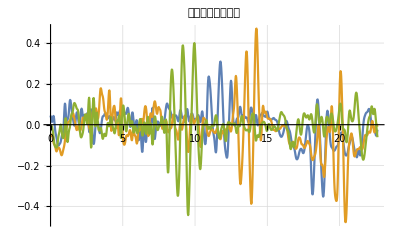

```mathematica
Manipulate[
(*r=1.5;*)
ListPlot[{Table[{x,(1+Tanh[(-x)/r+π])/2},{x,-100,100,.1}],
Table[{x,0},{x,0,2π*r,.1}],
Table[{x,Abs[Tanh[(-x)/r+π]/2]},{x,-2π*r,2π*r,.1}]},PlotLabel->2π*r,PlotRange->{{-100,100},{0,1}}]
,{r,0.1,50,.05}]
```

```mathematica
Manipulate[
(*r=1.5;*)
r=R/(2π);
ListPlot[{Table[{x,(1+Tanh[(-x)/r+π])/2},{x,-100,100,.1}],
Table[{x,0},{x,0,2π*r,.1}],
Table[{x,Abs[Tanh[(-x)/r+π]/2]},{x,-2π*r,2π*r,.1}]},PlotLabel->2π*r,PlotRange->{{-100,100},{0,1}}]
,{R,0.1,50,.05}]
```

```mathematica
Manipulate[
(*r=1.5;*)
ListPlot[Table[{x,(1+Tanh[4((x/r)-1)])/2},{x,-1,10,.1}],PlotLabel->r]
,{r,1,6,.1}]
```

```mathematica
Manipulate[
(*r=1.5;*)
ListPlot[{
Table[{d,80000((Tanh[π(c-π/2*d)/c]+1)/2)},{d,0,2*c,.0001}],
Table[{d,100*(1-d)/c},{d,0,2*c,.0001}]
},
PlotLabel->c,
PlotStyle->{Red,Blue,Magenta},
PlotRange->{{0,2*c},All}]
,{c,0.004/3,0.01,.001}]
```

```mathematica
0.004/3
```

0.00133333

```mathematica
N@Tanh[π]
```

0.996272